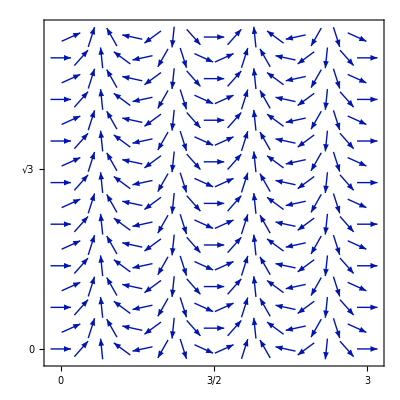

```mathematica
With[{q0=4 π/3{1,0},q1=4 π/3 RotationMatrix[-π/3*2].{1,0},q2=4 π/3*RotationMatrix[π/3*2].{1,0}},VectorPlot[Sum[{Cos[q.{x,y}],Sin[q.{x,y}]},{q,{q0}}],{x,0,3},{y,0,3},FrameTicks->{{0,3/2,6/2,9/2},{0,√3,2 √3}}]]
```

```mathematica
ListVectorPlot
```

```mathematica
n
```

```mathematica
√3*√3/2
```

3/2

```mathematica
S[x_,y_]:=Block[{q0=4 π/3{-1,0},q1,q2},q1=RotationMatrix[π*2/3].q0;q2=RotationMatrix[π*4/3].q0;Sum[{Cos[q.{x,y}],Sin[q.{x,y}]},{q,{q0,q1,q2}}]]
```

```mathematica
S[x_,y_]:=Block[{q0=4 π/3{-1,0},q1,q2},q1=RotationMatrix[π*2/3].q0;q2=RotationMatrix[π*4/3].q0;Sum[{Cos[q.{x,y}],Sin[q.{x,y}]},{q,{q0,q1,q2}}]]
```

```mathematica
S[0,0]
```

{1,0}

```mathematica
aM1={1,0};aM2={1/2,(√3)/2};
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,5},{h2,0,5}];Slist=Table[{aM1*h1+aM2*h2,S@@(aM1*h1+aM2*h2)},{h1,0,5},{h2,0,5}];
```

```mathematica
ptsf=Table[aM1*h1+aM2*h2,{h1,0,5,0.25},{h2,0,5,0.25}];Slistf=Table[{aM1*h1+aM2*h2,S@@(aM1*h1+aM2*h2)},{h1,0,5,0.25},{h2,0,5,0.25}];
```

```mathematica
Slistfmod=Table[Flatten@{aM1*h1+aM2*h2,Norm[S@@(aM1*h1+aM2*h2)]},{h1,0,5,0.05},{h2,0,5,0.05}];
```

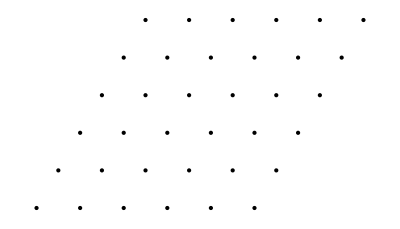

```mathematica
Graphics[Point/@pts]
```

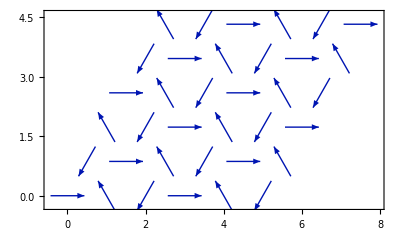

```mathematica
ListVectorPlot[Flatten[Slist,1],VectorPoints->All,AspectRatio->Automatic]
```

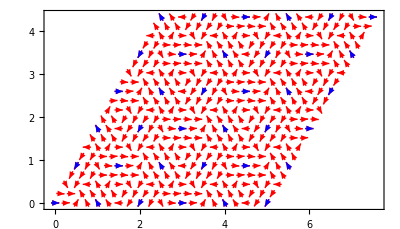

```mathematica
ListVectorPlot[{Flatten[Slistf,1],Flatten[Slist,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

```mathematica
ListDensityPlot[Flatten[Slistfmod,1],AspectRatio->Automatic,PlotLegends->Automatic]
```

-Graphics-

```mathematica
S@@(1/3*(aM1+aM2))
```

{0,0}

```mathematica
f
```

```mathematica
Slist//Dimensions
```

{6,6,2,2}

```mathematica
Flatten[Slist,1]//Dimensions
```

{36,2,2}